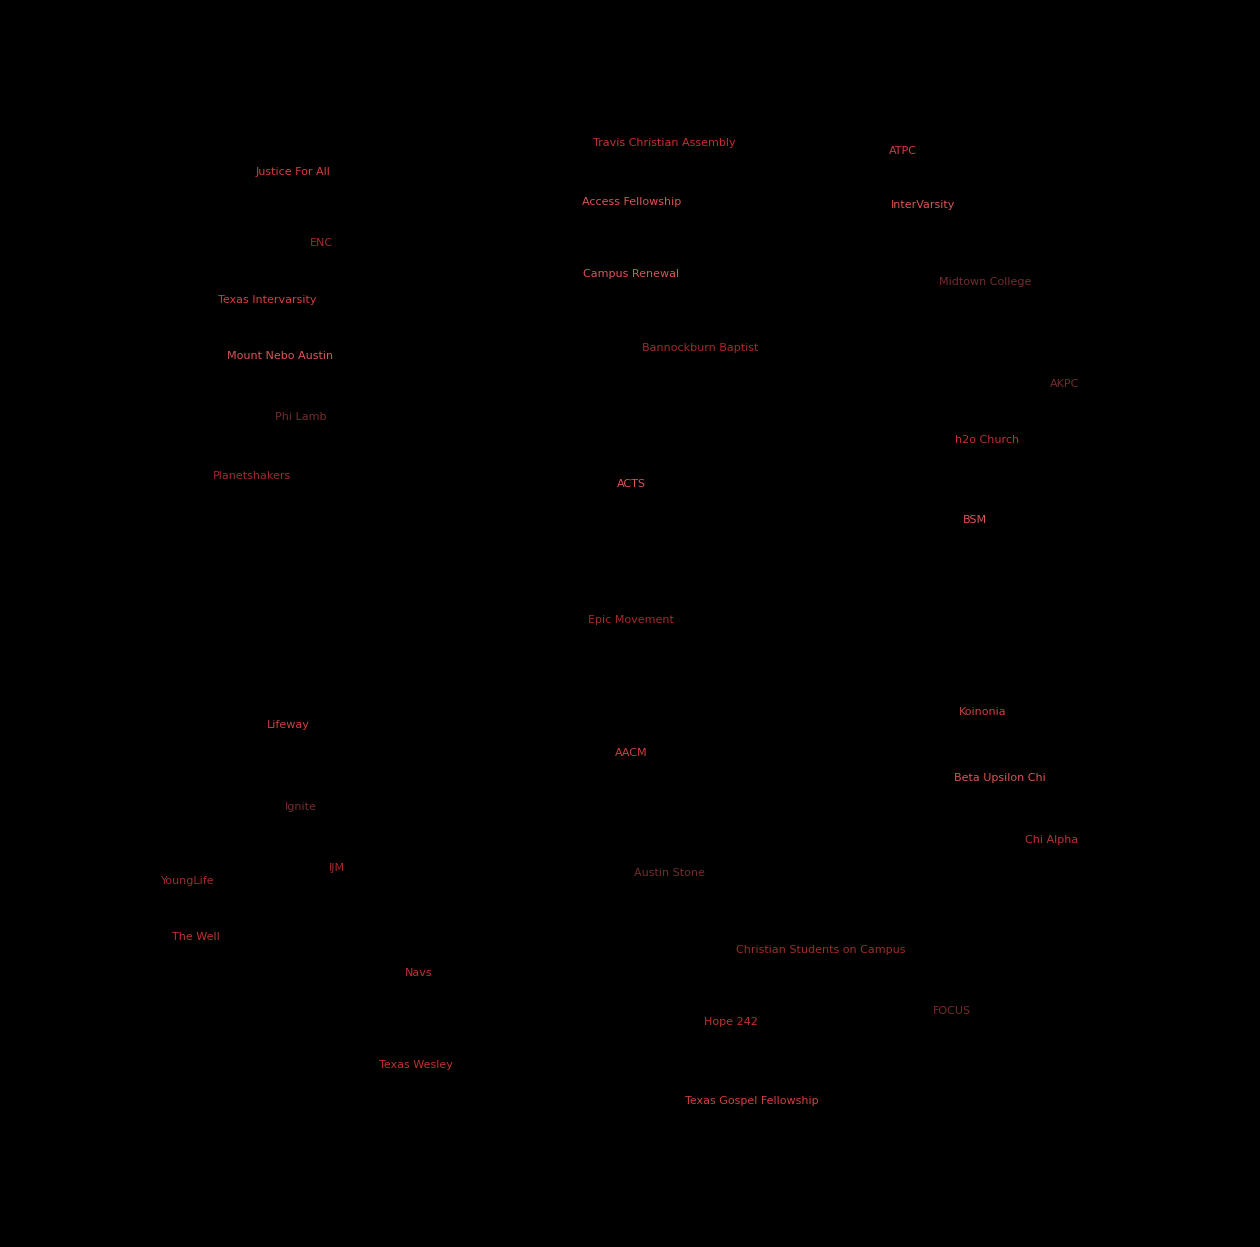

/Users/Evan/GitProjects/campusmap/RezWeekCal/wordcloud.png

Volunteer_Status.jpg

```mathematica
wc=WordCloud[
{54->"AACM",65->"ACTS",5->"AKPC",4->"ATPC",8->"Access Fellowship",32->"Austin Stone",23->"BSM",16->"Bannockburn Baptist",5->"Beta Upsilon Chi",15->"Campus Renewal",4->"Chi Alpha",4->"Christian Students on Campus",9->"ENC",38->"Epic Movement",3->"FOCUS",17->"Hope 242",1->"IJM",16->"Ignite",3->"InterVarsity",8->"Justice For All",15->"Koinonia",18->"Lifeway",1->"Midtown College",1->"Mount Nebo Austin",46->"Navs",9->"Phi Lamb",6->"Planetshakers",2->"Texas Gospel Fellowship",1->"Texas Intervarsity",10->"Texas Wesley",1->"The Well",2->"Travis Christian Assembly",1->"YoungLife",6->"h2o Church"},
Background->Transparent,ColorFunction->Reverse[Table[ColorData["CherryTones"][i],{i,0.1,.5,0.1}]],
WordSpacings->5,
ImageSize->1260]
Export["/Users/Evan/GitProjects/campusmap/RezWeekCal/wordcloud.png",wc,"PNG"]
SetDirectory["/Users/Evan/GitProjects/campusmap/RezWeekCal"];
Export["Volunteer_Status.jpg",ImageAssemble[{Import/@FileNames["*_cal.png"]}], ImageSize->1920]
```

```mathematica
CloudDeploy[FormFunction[{"profile"->"Image"},Block[{filter,img,size},

img = #profile;
filter=-Graphics-;
(* Crop the profile to the middle square *)
size=Min[ImageDimensions[img]];
img=ImageCrop[img,{size,size}];

(* Using the min ensures highest resolution *)
size=Min[size,ImageDimensions[filter]];

(* Scale images to the same size *)
img=ColorConvert[ImageResize[img,size],"Grayscale"];
filter=ImageResize[filter,size];

ImageAdjust[Blend[{img,filter}],{.1,.1}]]&,"PNG"],Permissions->"Public"]
```